{787.617,701.277,784.73,750.299,758.725,769.301,838.245,770.952,761.532,747.649,761.769,769.86,751.642,847.041,751.432,750.614,750.115,763.795,99964,735.805,756.144,818.275,771.583,774.219,750.112,693.478,719.708,712.172,721.912,766.037,811.351,730.28,783.391,757.684,735.787,764.216,817.5}
 |  |  |  |

761.156

0.05006

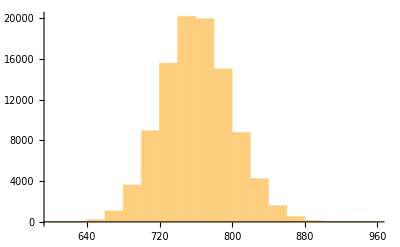

```mathematica
σ=0.2; (*Volatility (Standard deviation) of return rate per time unit.*)
T1=0.25;  (*Amount of time*)
α=0; (*Expected rate of return per time unit*)
δ=0; (*Expected dividend rate per time unit*)
initialStockPrice=761;
firstQuartersimulatedFutureStockPrices=Table[
randomDraw=RandomVariate[NormalDistribution[0,1]];
initialStockPrice*E^((α-δ-1/2*σ^2)T1+σ*Sqrt[T1]*randomDraw)
,{100000}
];
secondQuartersimulatedFutureStockPrices=Table[
randomDraw=RandomVariate[NormalDistribution[0,1]];
initialStockPrice*E^((α-δ-1/2*σ^2)T1+σ*Sqrt[T1]*randomDraw)
,{100000}
];
thirdQuartersimulatedFutureStockPrices=Table[
randomDraw=RandomVariate[NormalDistribution[0,1]];
initialStockPrice*E^((α-δ-1/2*σ^2)T1+σ*Sqrt[T1]*randomDraw)
,{100000}
];
forthQuartersimulatedFutureStockPrices=Table[
randomDraw=RandomVariate[NormalDistribution[0,1]];
initialStockPrice*E^((α-δ-1/2*σ^2)T1+σ*Sqrt[T1]*randomDraw)
,{100000}
];

simulatedFutureStockPrices=N[firstQuartersimulatedFutureStockPrices+secondQuartersimulatedFutureStockPrices+thirdQuartersimulatedFutureStockPrices+forthQuartersimulatedFutureStockPrices]/4


(*Expected future stock price should be Subscript[S, 0] ⅇ^αT*)
Mean[simulatedFutureStockPrices]

StandardDeviation[Log[simulatedFutureStockPrices]]
(*Notice it is skewed right.*)
Histogram[simulatedFutureStockPrices]
```

```mathematica
0.2
```

FinancialDerivative::checkc: The contract specification {Asian,Call} does not match any available pattern.

```mathematica
FinancialDerivative[{"AsianArithmetic","Call"},{"StrikePrice"->50.,"Expiration"->1},{"InterestRate"->0,"Volatility"->0.2,"CurrentPrice"->761,"Dividend"->0}]
```

FinancialDerivative::checkc: The contract specification {AsianArithmetic,Call} does not match any available pattern.

FinancialDerivative[{AsianArithmetic,Call},{StrikePrice→50.,Expiration→1},{InterestRate→0,Volatility→0.2,CurrentPrice→761,Dividend→0}]